3/4

3

0

4/5

-3^(3/4) ⅇ^(3 x) (-1+GammaRegularized[-3/4,3 x])

3^(3/4) ⅇ^(3 x) GammaRegularized[-3/4,0,3 x]

-1/(x^(3/4) Gamma[1/4])-3^(3/4) ⅇ^(3 x) (-1+GammaRegularized[-3/4,3 x])

3^(3/4) ⅇ^(3 x) GammaRegularized[1/4,0,3 x]

3^(3/4) ⅇ^(3 x)

asymptotics-> x->Infinity

3^(3/4) ⅇ^(3 x)

3^(3/4) ⅇ^(3 x)

3^(3/4) ⅇ^(3 x)

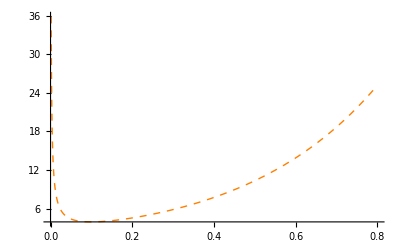

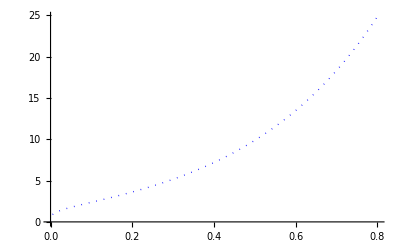

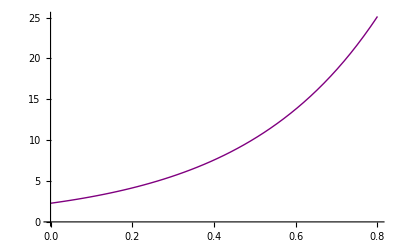

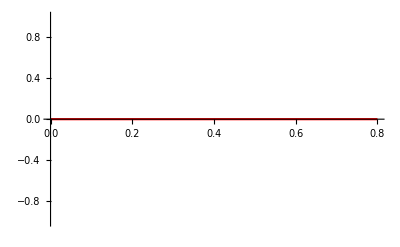

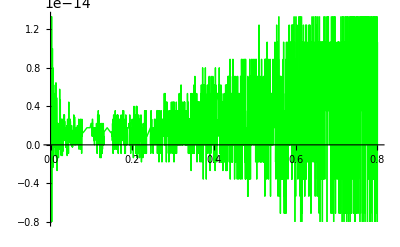

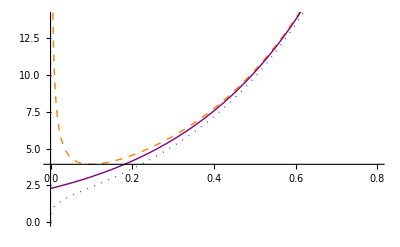

```mathematica
(*Input parameters*)
alpha=75/100                               (*alpha*)
k=3                             (*k>0 in e^(k x)*)
lb=0                            (*plot lower bound*)
ub=8/10                         (*plot upper bound*)
(*Riemann official and (3.82)*)
rieMat=FractionalD[Exp[k x],{x,alpha}]
rie382=x^(-alpha) MittagLefflerE[1,1-alpha,k x]
(*Caputo official and (3.91)*)
capMat=CaputoD[Exp[k x],{x,alpha}]
cap391=k x^(1-alpha) MittagLefflerE[1,2-alpha,k x]
(*Liouville (3.92)*)
lio392=k^alpha Exp[k x]
(*check asymptotics for x->Infinity*)
Print["asymptotics-> x->Infinity"]
Asymptotic[rieMat,x->Infinity]
Asymptotic[capMat,x->Infinity]
Asymptotic[lio392,x->Infinity]
(*pot routines*)
pr1=Plot[rieMat,{x,lb,ub},PlotStyle->{Orange,Dashed,Thick}]
pc1=Plot[capMat,{x,lb,ub},PlotStyle->{Blue,Dotted,Thick}]
pl1=Plot[lio392,{x,lb,ub},PlotStyle->{Purple,Thick}]
(*errors:official versus derived in ex(3.4.2)*)
psr=Plot[rieMat-rie382,{x,lb,ub},PlotStyle->{Red}]
psc=Plot[capMat-cap391,{x,lb,ub},PlotStyle->{Green,Thick}]

(*final output*)
Show[{pr1,pc1,pl1},PlotRange->{{lb,ub},{0,14}}]
```